Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 5

Metoda kolejnych przybliżeń

## Równanie Fredholma II rodzaju

### Zadanie 1

Wyznaczyć metodą kolejnych przybliżeń rozwiązanie przybliżone y_n równania

y(x)=ⅇ^x-1/4∫_0^1 (x ⅇ^t y(t))ⅆt

Argument:  n

Sprawdzić, czy metodę można zastosować. 
Wyznaczyć rozwiązanie dla kilku wartości n. 
Na tej podstawie odgadnąć rozwiązanie dokładne i sprawdzić jego poprawność.

### Zadanie 2

Wyznaczyć rozwiązania przybliżone y_n dla  n=2,4,6,8, równania:

y(x)=sin x + (x-1)/4+1/4∫_0^(π/2) (t-x)  y(t)ⅆt.

Utworzyć wykresy porównujące rozwiązanie przybliżone z rozwiązaniem dokładnym, którym jest funkcja y(x)=sin x, np.  w postaci:

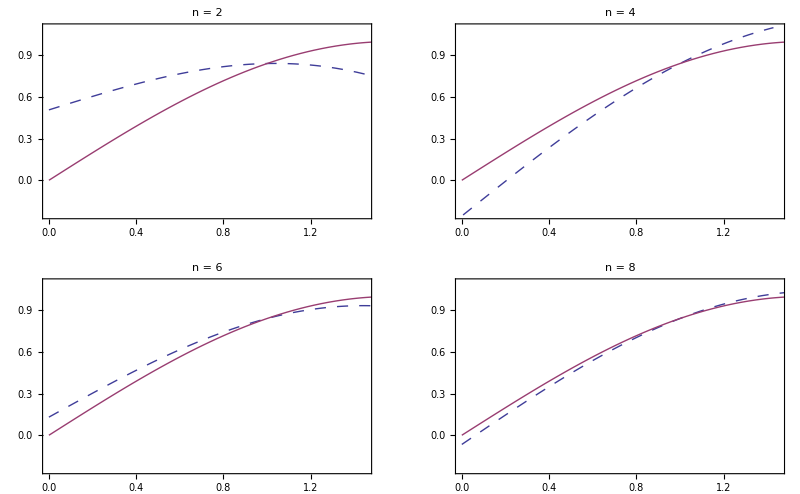

```mathematica
Clear[mkpf2];
mkpf2[k_,f_,a_,b_,λ_,n_,z_Symbol] := Module[{ϕ,i, wyn=0,x,t},
(* Definicja funkcji ϕ *)
ϕ[0][x_] := f[x];
Do[ϕ[i][x_]=Integrate[k[x,t]*ϕ[i-1][t],{t,a,b}],{i,1,n}];
(* Utworzenie rozwiązania przybliżonego *)
Do[wyn=wyn+λ^i*ϕ[i][z],{i,0,n}];
(* Wypisanie rozwiązania przybliżonego *)
Return[wyn]
];
```

```mathematica
(* Zadanie 1 *)
(* Sprawdzam,czy metodę można zastosować *)
a=0;
b=1;
λ = -1/4;
f[x_] := ⅇ^x;
k[x_,t_] := x* ⅇ^t;

M =MaxValue[{x* ⅇ^t,{0 <= x <= 1,0<=t<=1}},{x,t}];

Abs[λ] < 1/(M(b-a)) (* Jeżeli jest True to możemy zastosować metodę *)
```

True

```mathematica
(* n = 10 *)
n = 10;
mkpf2[k,f,a,b,λ,n, x]
```

ⅇ^x-(209715 (-1+ⅇ^2) x)/2097152

```mathematica
(* n = 20 *)
n = 20;
mkpf2[k,f,a,b,λ,n, x]
```

ⅇ^x-(219902325555 (-1+ⅇ^2) x)/2199023255552

```mathematica
(* n = 50 *)
n = 50;
mkpf2[k,f,a,b,λ,n, x]
```

ⅇ^x-(253530120045645880299340641075 (-1+ⅇ^2) x)/2535301200456458802993406410752

```mathematica
(* n = 1000 *)
n = 1000;
mkpf2[k,f,a,b,λ,n, x];
```

```mathematica
(* Odgaduję rozwiązanie dokładne: y = ⅇ^x-((-1+ⅇ^2) x)/10;*)
```

```mathematica
(* Sprawdzam dokładność *)
```

```mathematica
g[x_] := ⅇ^x-((-1+ⅇ^2) x)/10;
```

```mathematica
g[x] == ⅇ^x-1/4∫_0^1 (x ⅇ^t g[t])ⅆt // Simplify (* Jeżeli zwróci True to odgadnięte rozwiązanie jest rozwiązaniem dokładnym*)
```

1/10 (-1+ⅇ^2) x+Sin[x]==ⅇ^x

```mathematica
(* Zadanie 2 *)
y[x]=Sin[x] + (x-1)/4+1/4∫_0^(π/2) (t-x)  y[t]ⅆt;
(* Funkcja dokładna *)
```

```mathematica
g[x]=Sin[x];

(* Wyniki dla n = 2,4,6,8 *)
Clear[a,b,λ,f,k, M]
(* Sin[x] + (x-1)/4+1/4∫_0^(π/2) (t-x)y[t]ⅆt *)
a=0;
b=π/2;
λ = 1/4;
f[x_] := Sin[x] + (x-1)/4;
k[x_,t_] := (t-x);

M = MaxValue[{t-x,0<=t<=π/2},{x,t}]
Abs[λ] < 1/(M(b-a)) (* Jeżeli jest True to możemy zastosować metodę *)
```

∞

False

```mathematica
n2 = mkpf2[k,f,a,b,λ,2, x]; // Simplify
n4 = mkpf2[k,f,a,b,λ,4, x];// Simplify
n6 = mkpf2[k,f,a,b,λ,6, x];// Simplify
n8 = mkpf2[k,f,a,b,λ,8, x];// Simplify
```

```mathematica
p1 = Plot[{n2,Sin[x]},{x,0,π/2}, PlotLabel->"n = 2", PlotStyle->{Dashed,Red}];
p2 = Plot[{n4,Sin[x]},{x,0,π/2}, PlotLabel->"n = 4", PlotStyle->{Dashed,Red}];
p3 = Plot[{n6,Sin[x]},{x,0,π/2}, PlotLabel->"n = 6", PlotStyle->{Dashed,Red}];
p4 = Plot[{n8,Sin[x]},{x,0,π/2}, PlotLabel->"n = 8", PlotStyle->{Dashed,Red}];
```

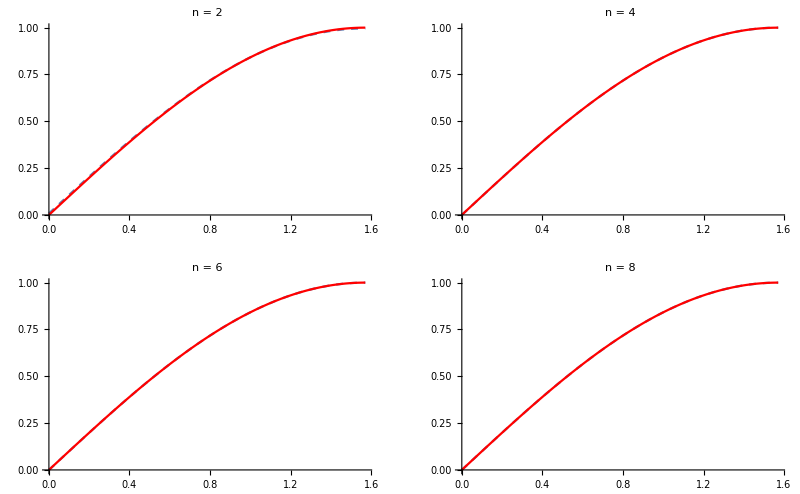

```mathematica
GraphicsGrid[{{p1,p2},{p3,p4}}, Frame -> All]
```